```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
Show[
ListLinePlot[Table[{i,Abs[fz1[i,0,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[fz1[i,0.95qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fz1[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotStyle->Red],

ListLinePlot[Table[{i,Abs[fz1[i,7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotStyle->Green],PlotRange->{{0.01,5.5},{0,1}},AxesOrigin->{0,0}
]
]
```

$Aborted

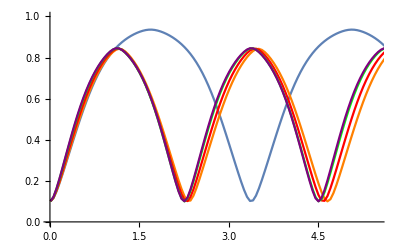

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
Show[
ListLinePlot[Table[{i,Abs[fz1[i,qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[fz1[i,1.2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.0625],1,0.0625,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.0625],1,0.0625]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fz1[i,1.2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fz1[i,1.2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]]},{i,0.01,7,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Abs[fz1[i,1.2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.2],1,0.2,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.2],1,0.2]]},{i,0.01,7,0.05}],PlotStyle->Purple],
PlotRange->{{0.01,5.5},{0,1}},AxesOrigin->{0,0}
]
]
```

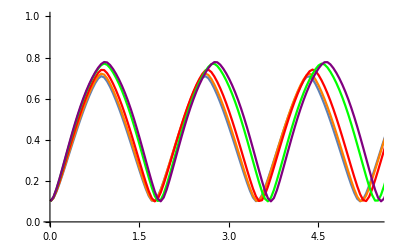

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
Show[
ListLinePlot[Table[{i,Abs[fz1[i,70,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[fz1[i,70,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.0625],1,0.0625]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fz1[i,70,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fz1[i,70,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]]},{i,0.01,7,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Abs[fz1[i,70,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.2],1,0.2]]},{i,0.01,7,0.05}],PlotStyle->Purple],
PlotRange->{{0.01,5.5},{0,1}},AxesOrigin->{0,0}
]
]
```

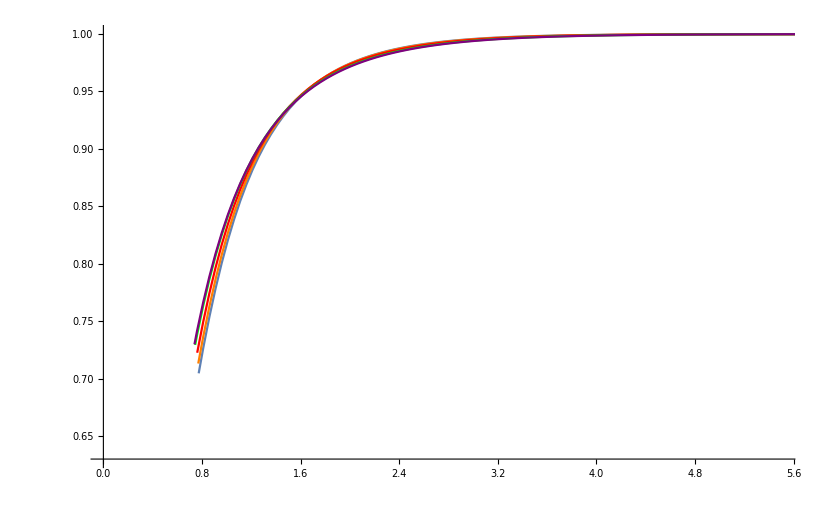

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
Show[
ListLinePlot[Table[{i,Abs[fz1[i,10^-6,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[fz1[i,10^-6,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.0625],1,0.0625]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fz1[i,10^-6,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fz1[i,10^-6,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]]},{i,0.01,7,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Abs[fz1[i,10^-6,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.2],1,0.2]]},{i,0.01,7,0.05}],PlotStyle->Purple],
PlotRange->{{0.01,5.5},{0.63,1}},AxesOrigin->{0,0.63}
]
]
```

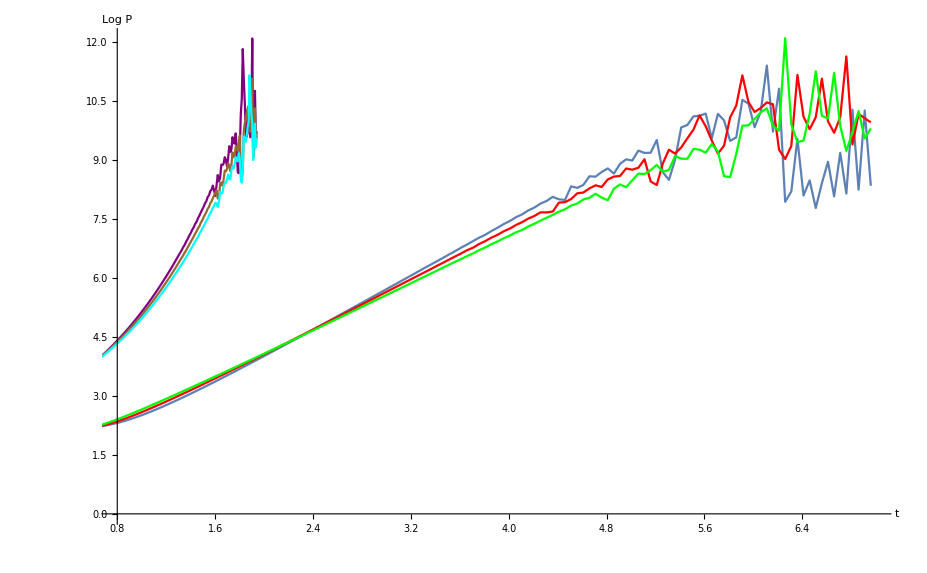

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[1/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,Abs[pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]//Log},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]]//Log},{i,0.01,7,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Abs[pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.19],1,0.19,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.19],1,0.19]]},{i,0.01,7,0.05}]//Log,PlotStyle->Purple],
ListLinePlot[Table[{i,Abs[pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.23],1,0.23,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.23],1,0.23]]},{i,0.01,7,0.05}]//Log,PlotStyle->Brown],
ListLinePlot[Table[{i,Abs[pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.245],1,0.245,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.245],1,0.245]]},{i,0.01,7,0.05}]//Log,PlotStyle->Cyan],
PlotRange->{{0.8,7},All},AxesOrigin->{0.8,0},AxesLabel->{t,Log P}
]
]
```

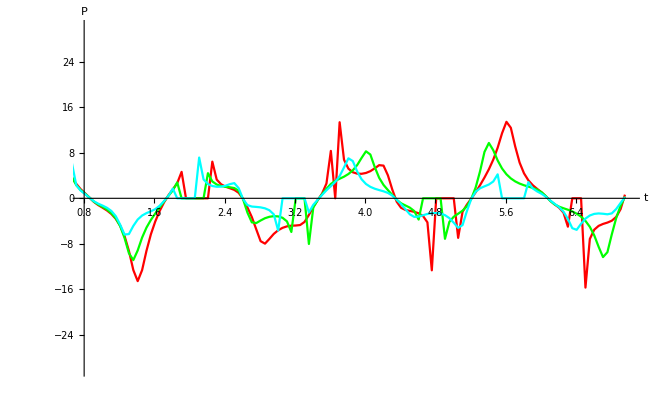

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,70,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[1/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,Re[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Re[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1875],1,0.1875]]},{i,0.01,7,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Re[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.245],1,0.245,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.245],1,0.245]]},{i,0.01,7,0.05}],PlotStyle->Cyan],
PlotRange->{{0.8,7},{-30,30}},AxesOrigin->{0.8,0},AxesLabel->{t,P}
]
]
```

```mathematica
Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)/Sqrt[(1+Sqrt[1+4λ])/2]//TraditionalForm
```

(√2 √(f(zs,1/zp,μ,l,λ,k)))/(√(√(4 λ+1)+1) μ zs (1-zs/zp))

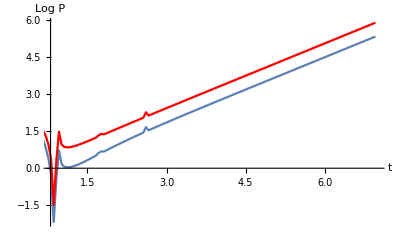

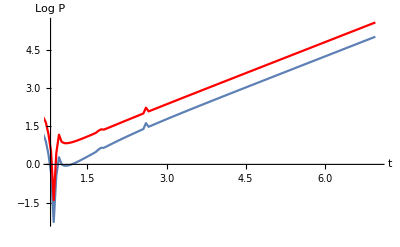

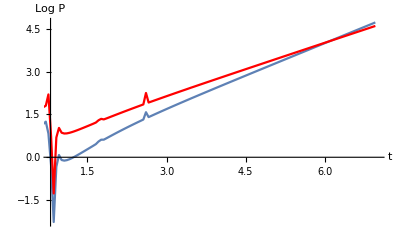

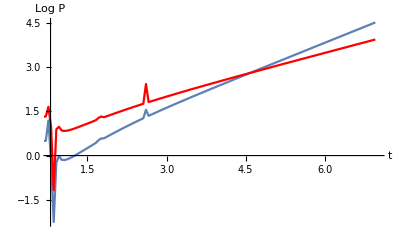

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,βpz,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)*Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,70,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[1/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
βpz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]//Log},{i,0.01,7,0.05}],PlotStyle->Red],
PlotRange->{{0.8,7},All},AxesOrigin->{0.8,0},AxesLabel->{t,Log P}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]//Log},{i,0.01,7,0.05}],PlotStyle->Red],
PlotRange->{{0.8,7},All},AxesOrigin->{0.8,0},AxesLabel->{t,Log P}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.19],1,0.19,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.19],1,0.19]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.19],1,0.19,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.19]]//Log},{i,0.01,7,0.05}],PlotStyle->Red],
PlotRange->{{0.8,7},All},AxesOrigin->{0.8,0},AxesLabel->{t,Log P}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.22],1,0.22,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.22],1,0.22]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.22],1,0.22,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.22]]//Log},{i,0.01,7,0.05}],PlotStyle->Red],
PlotRange->{{0.8,7},All},AxesOrigin->{0.8,0},AxesLabel->{t,Log P}
]];
]
```

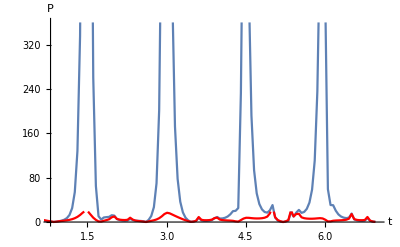

-Graphics-

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,βpz,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,70,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[1/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
βpz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]},{i,0.01,7,0.05}],PlotStyle->Red],
PlotRange->{{0.8,7},All},AxesOrigin->{0.8,0},AxesLabel->{t,P}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]},{i,0.01,7,0.05}],PlotStyle->Red],
PlotRange->{{0.8,7},All},AxesOrigin->{0.8,0},AxesLabel->{t,P}
]];
]
```

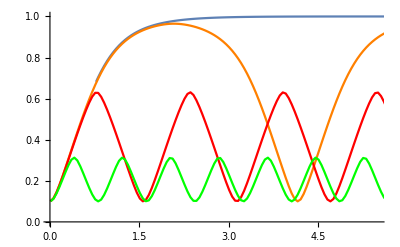

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
Show[
ListLinePlot[Table[{i,Abs[fz1[i,10^(-6),1,0.1,0.75μextreme[Sqrt[8Pi],1,1,-0.125],1,-0.125]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[fz1[i,0.95qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,-0.125],1,-0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,-0.125],1,-0.125]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fz1[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,-0.125],1,-0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,-0.125],1,-0.125]]},{i,0.01,7,0.05}],PlotStyle->Red],

ListLinePlot[Table[{i,Abs[fz1[i,7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,-0.125],1,-0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,-0.125],1,-0.125]]},{i,0.01,7,0.05}],PlotStyle->Green],PlotRange->{{0.01,5.5},{0,1}},AxesOrigin->{0,0}
]
]
```

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[1/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Print[pz[3,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]];
Print[pz[2,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1],1,0.1,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1],1,0.1]];
Print[pz[7,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.1],1,0.1,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.1],1,0.1]];
Print[pz[4.5,0.7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.2],1,0.2,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.2],1,0.2]];
]
```

304.079+0. ⅈ

57.539+0. ⅈ

177916.-1.05341 ⅈ

2360.67+0. ⅈ